```mathematica
Reduce[M[t]==M[t-(50/60)]&&0<t<6,t]//N
```

t==3.75||t==0.416667||t==2.08333||t==5.41667

```mathematica
M[t_]:=(1/2)-(1/2) Cos[(3*Pi/5)*t]
```

x==-2 ArcTan[(-1+Cos[1]) Csc[1]-√(1+Cot[1]^2-2 Cot[1] Csc[1]+Csc[1]^2)]||x==2 π-2 ArcTan[(-1+Cos[1]) Csc[1]+√(1+Cot[1]^2-2 Cot[1] Csc[1]+Csc[1]^2)]

{{x→2.0708},{x→5.21239}}

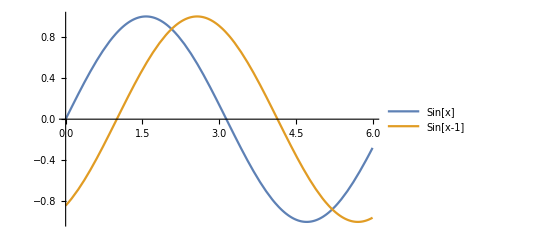

```mathematica
eq = Sin[x] == Sin[x-1];

Reduce[eq && 0 <= x <= 6, x, Reals]

NSolve[Sin[x] == Sin[x-1] && 0 <= x <= 6, x]

Plot[{Sin[x], Sin[x-1]}, {x, 0, 6}, PlotLegends -> {"Sin[x]", "Sin[x-1]"}]
```

(5 ArcCos[-4/5])/(3 π)≤t≤(10 π-5 ArcCos[-4/5])/(3 π)||(10 π+5 ArcCos[-4/5])/(3 π)≤t≤(20 π-5 ArcCos[-4/5])/(3 π)

(5 ArcCos[-4/5])/(3 π)≤t≤(10 π-5 ArcCos[-4/5])/(3 π)||(10 π+5 ArcCos[-4/5])/(3 π)≤t≤(20 π-5 ArcCos[-4/5])/(3 π)

NSolve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

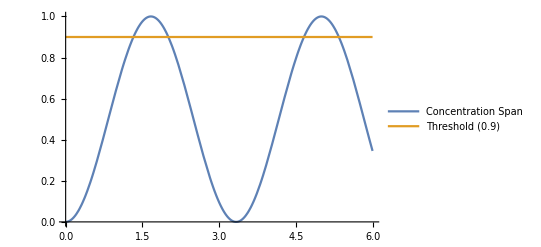

```mathematica
m[t_]:=1/2-1/2 Cos[(3 Pi/5) t]

threshold = 9/10;

highConcentrationTimes=Reduce[m[t]>=threshold&&0<=t<=6,t,Reals]

highConcentrationTimes

NSolve[m[t]>=threshold&&0<=t<=6,t]
Plot[{m[t],threshold},{t,0,6},PlotLegends->{"Concentration Span","Threshold (0.9)"}]
```